```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
HedgeChart[stock_,inverse_,start_,end_]:=Module[{s1,s2,portfolio},
s1=NormalizeData[stock,start,end];
s2=NormalizeData[inverse,start,end];
portfolio=Transpose@{s2[[All,1]],Mean/@Transpose@{s1[[All,2]],s2[[All,2]]}};
DateListPlot[{s1,s2,portfolio},PlotLegends->{stock,inverse,stock<>" & "<>inverse},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[3,"Years"]];
end=Today
```

Tue 12 Apr 2016

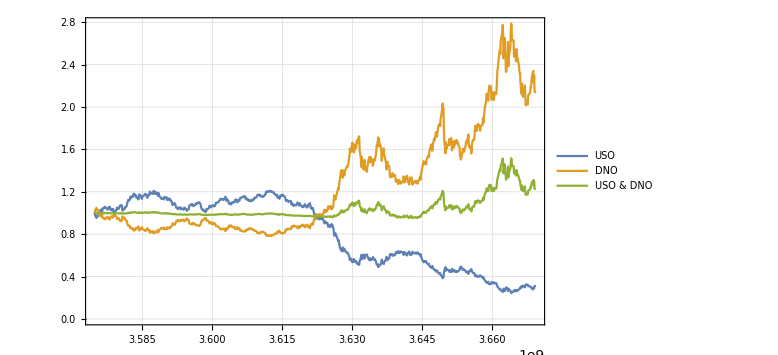

```mathematica
chart1=HedgeChart["USO","DNO",start,end]
(*chart2=HedgeChart["UCO","SCO",start,end]*)
(*chart3=HedgeChart["UWTI","DWTI",start,end]*)
```

```mathematica
(*Export[NotebookDirectory[]<>"USO.png",Magnify@chart1];
Export[NotebookDirectory[]<>"UCO.png",Magnify@chart2];Export[NotebookDirectory[]<>"UWTI.png",Magnify@chart3];*)
```

```mathematica
(*chart1=HedgeChart["IYE","DDG",start,Today];
chart2=HedgeChart["DIG","DUG",start,Today];
Export[NotebookDirectory[]<>"iye_ddg.png",Magnify@chart1];
Export[NotebookDirectory[]<>"dig_dug.png",Magnify@chart2];*)
```

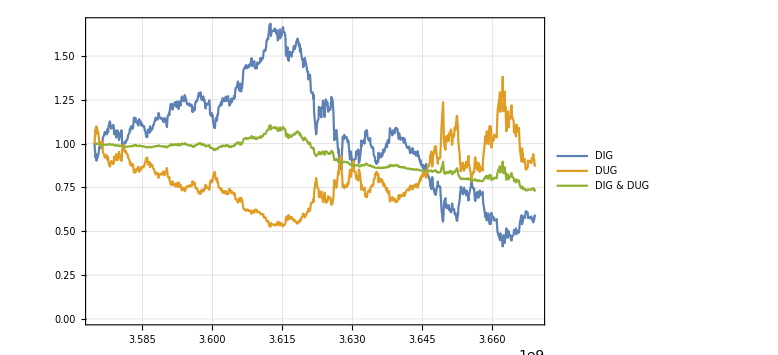

```mathematica
HedgeChart["DIG","DUG",start,end]
```

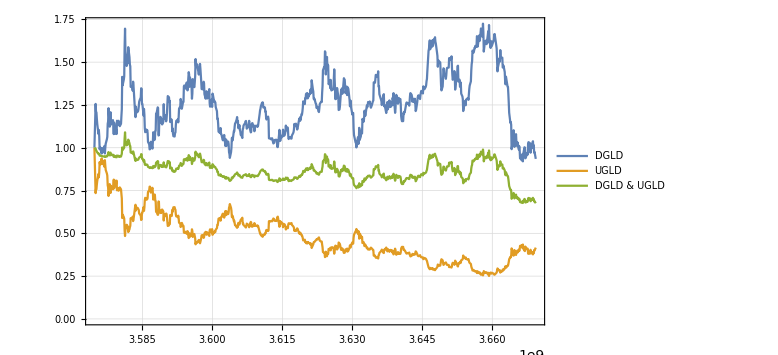

```mathematica
HedgeChart["DGLD","UGLD",start,end]
```

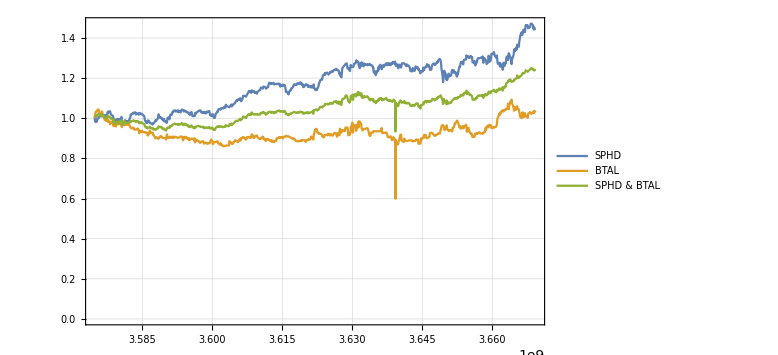

```mathematica
btal=HedgeChart["SPHD","BTAL",start,end]
```

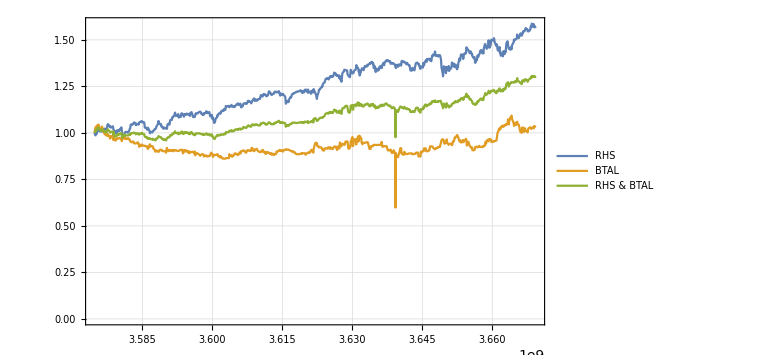

```mathematica
rhs=HedgeChart["RHS","BTAL",start,end]
```

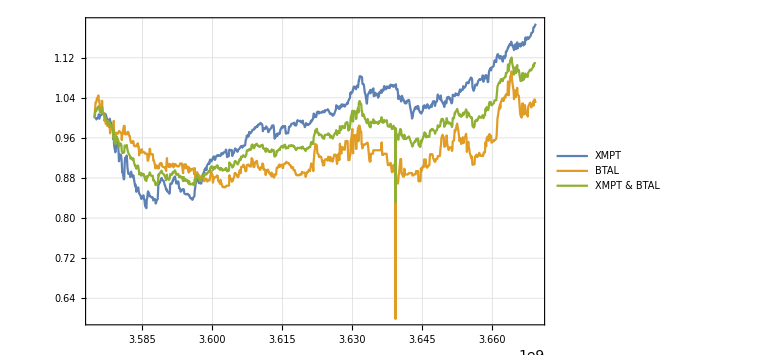

```mathematica
HedgeChart["XMPT","BTAL",start,end]
```

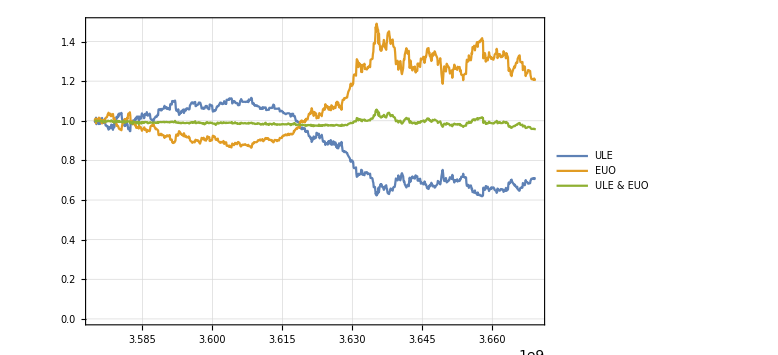

```mathematica
euo=HedgeChart["ULE","EUO",start,end]
```

```mathematica
(*Export[NotebookDirectory[]<>"btal.png",Magnify@btal];
Export[NotebookDirectory[]<>"euo.png",Magnify@euo];*)
```

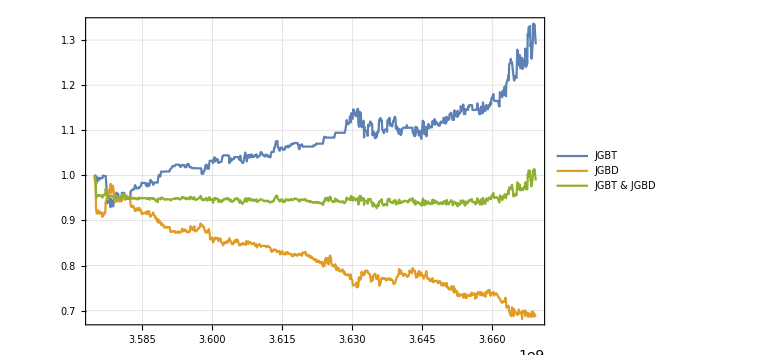

```mathematica
HedgeChart["JGBT","JGBD",start,end]
```

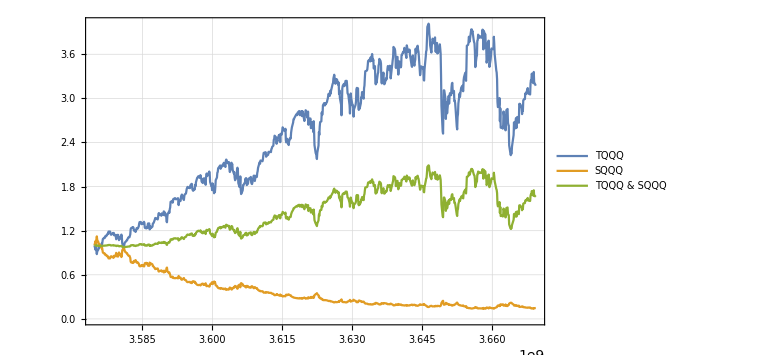

```mathematica
HedgeChart["TQQQ","SQQQ",start,end]
```

```mathematica
NormalizeData[symbol_,start_,end_]:=FinancialData[symbol,{start,end}]//Transpose@{#[[All,1]],#[[All,2]]/First@#[[All,2]]}&
BTALChart[stock_,inverse_,start_,end_]:=Module[{btal,invalid,s1,s2,portfolio,portfolio2},
btal=NormalizeData["BTAL",start,end];
invalid=First@FirstPosition[btal[[All,1]],_?(#=={2015,4,29}&)];
btal=Delete[btal,invalid];
s1=NormalizeData[stock,start,end]//Delete[#,invalid]&;
s2=NormalizeData[inverse,start,end]//Delete[#,invalid]&;
portfolio=Transpose@{s1[[All,1]],Mean/@Transpose@{btal[[All,2]],s1[[All,2]]}};
portfolio2=Transpose@{s1[[All,1]],Mean/@Transpose@{s2[[All,2]],s1[[All,2]]}};
DateListPlot[{btal,s1,s2,portfolio,portfolio2},PlotLegends->{"BTAL",stock,inverse,"BTAL & "<>stock,inverse<>" & "<>stock},PlotTheme->"Detailed",ImageSize->Large,BaseStyle->{FontSize->20},PlotRange->All]
]
```

```mathematica
start=DatePlus[Today,-Quantity[3,"Years"]];
end=Today;
chart1=BTALChart["SPY","SH",start,end];
chart2=BTALChart["QQQ","PSQ",start,end];
```

```mathematica
(*Export[NotebookDirectory[]<>"chart1.png",Magnify@chart1];
Export[NotebookDirectory[]<>"chart2.png",Magnify@chart2];*)
```